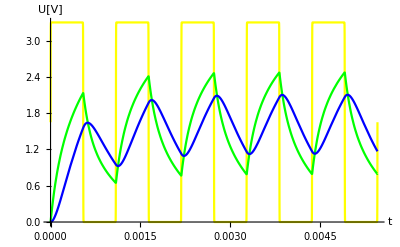

```mathematica
ClearAll["Global`*"]

uzel1 = 0==iR1[t]+iUz[t];
uzel2 = iR1[t]==iR2[t]+iC1[t];
uzel3 = iR2[t]==iC2[t]+iR3[t];
rez1 = u1[t]-u2[t]==R1*iR1[t];
rez2 = u2[t]-u3[t]==R2*iR2[t];
rez3 = u3[t]==R3*iR3[t];
kond1 = iC1[t]==C1*u2'[t];
kond2 = iC2[t]==C2*u3'[t];
pp1 = u2[0]==0;
pp2=u3[0]==0;
zdroj = uZ[t]==u1[t];

rovnice = {uzel1,uzel2,uzel3,rez1, rez2,rez3,kond1, kond2, pp1,pp2,zdroj};
nezname = {u1[t],u2[t],u3[t],iUz[t],iR1[t],iR2[t], iR3[t],iC1[t],iC2[t]};
soucastky = {R1-> 10000,R2->10*10^3,R3->1*10^6,C1->33*10^-9, C2->22*10^-9};

(* Definice zdroje napeti *)
amplituda = 3.3;
frekvence = 917;
perioda = 1/frekvence;
tmax = 5*perioda;
uZ[t_]:=amplituda*(1+Tanh[100*Sin[2*π*frekvence*t]])/2

Plot[uZ[t],{t,0,tmax}];

reseni = NDSolve[rovnice/.soucastky, nezname,{t,0,tmax}];

Plot[{u1[t]/.reseni[[1]],u2[t]/.reseni[[1]],u3[t]/.reseni[[1]]},{t,0,tmax},AxesLabel->{"t","U[V]"},PlotStyle->{Yellow,Green,Blue}]
```